```mathematica
xValues1 ={15,14.75,14.5,14.25,14,13.75,13.5,13.25,13,12.75,12.5,12.25,12,11.75,11.5,11}
```

{15,14.75,14.5,14.25,14,13.75,13.5,13.25,13,12.75,12.5,12.25,12,11.75,11.5,11}

```mathematica
{0.,0.1,0.2,0.30000000000000004,0.4,0.5,0.6000000000000001,0.7000000000000001,0.8,0.9,1.,1.1,1.2000000000000002,1.3,1.4}
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4}

```mathematica
yValues1 = {5,5,5,4.96,4.28,2.18,0.454,0.042,0.011,0.011,0.011,0.011,0.008,0.008,0.007,0.007}/5
```

{1,1,1,0.992,0.856,0.436,0.0908,0.0084,0.0022,0.0022,0.0022,0.0022,0.0016,0.0016,0.0014,0.0014}

```mathematica
data1 = Partition[Riffle[xValues1, yValues1], 2]
```

{{15,1},{14.75,1},{14.5,1},{14.25,0.992},{14,0.856},{13.75,0.436},{13.5,0.0908},{13.25,0.0084},{13,0.0022},{12.75,0.0022},{12.5,0.0022},{12.25,0.0022},{12,0.0016},{11.75,0.0016},{11.5,0.0014},{11,0.0014}}

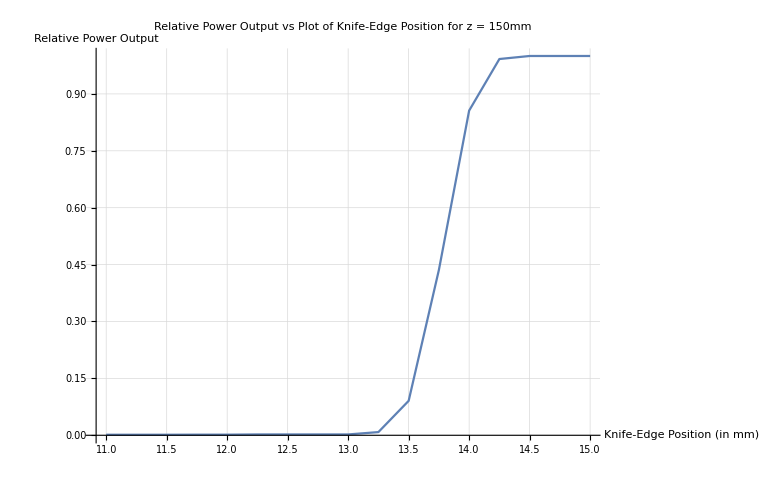

```mathematica
ListPlot[data1, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 150mm", GridLines->Automatic]
```

```mathematica
xValues2 = Range[11,9, -0.1]
```

{11.,10.9,10.8,10.7,10.6,10.5,10.4,10.3,10.2,10.1,10.,9.9,9.8,9.7,9.6,9.5,9.4,9.3,9.2,9.1,9.}

```mathematica
yValues2 = {6.47,6.45,6.37,6.2,5.84,5.33,4.47,3.39,2.3,1.38,0.784,0.351,0.135,0.052,0.029,0.015,0.012,0.010,0.010,0.010,0.010}/6.47
```

{1.,0.996909,0.984544,0.958269,0.902628,0.823802,0.690881,0.523957,0.355487,0.213292,0.121175,0.0542504,0.0208655,0.00803709,0.00448223,0.00231839,0.00185471,0.0015456,0.0015456,0.0015456,0.0015456}

```mathematica
data2 = Partition[Riffle[xValues2, yValues2], 2]
```

{{11.,1.},{10.9,0.996909},{10.8,0.984544},{10.7,0.958269},{10.6,0.902628},{10.5,0.823802},{10.4,0.690881},{10.3,0.523957},{10.2,0.355487},{10.1,0.213292},{10.,0.121175},{9.9,0.0542504},{9.8,0.0208655},{9.7,0.00803709},{9.6,0.00448223},{9.5,0.00231839},{9.4,0.00185471},{9.3,0.0015456},{9.2,0.0015456},{9.1,0.0015456},{9.,0.0015456}}

```mathematica
{{11.,6.47},{10.9,6.45},{10.8,6.37},{10.7,6.2},{10.6,5.84},{10.5,5.33},{10.4,4.47},{10.3,3.39},{10.2,2.3},{10.1,1.38},{10.,0.784},{9.9,0.351},{9.8,0.135},{9.7,0.052},{9.6,0.029},{9.5,0.015},{9.4,0.012},{9.3,0.01},{9.2,0.01},{9.1,0.01},{9.,0.01}}
```

{{11.,6.47},{10.9,6.45},{10.8,6.37},{10.7,6.2},{10.6,5.84},{10.5,5.33},{10.4,4.47},{10.3,3.39},{10.2,2.3},{10.1,1.38},{10.,0.784},{9.9,0.351},{9.8,0.135},{9.7,0.052},{9.6,0.029},{9.5,0.015},{9.4,0.012},{9.3,0.01},{9.2,0.01},{9.1,0.01},{9.,0.01}}

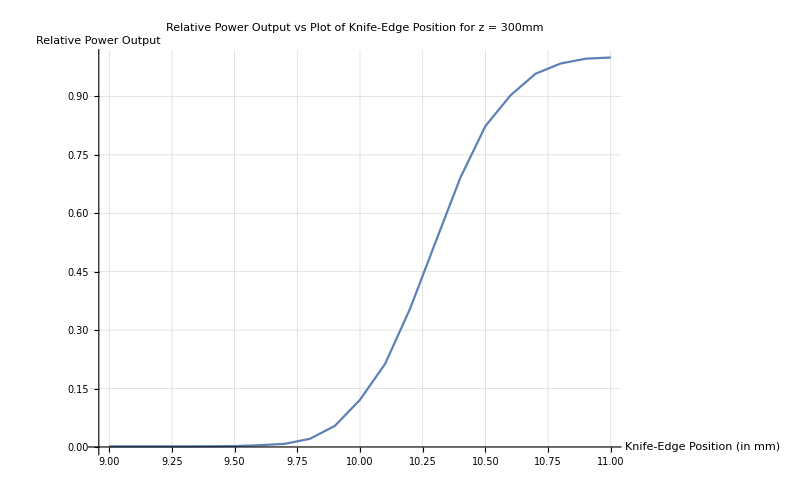

```mathematica
ListPlot[data2, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 300mm", GridLines->Automatic]
```

```mathematica
xValues3 = Range[16, 13.5, -0.1]
```

{16.,15.9,15.8,15.7,15.6,15.5,15.4,15.3,15.2,15.1,15.,14.9,14.8,14.7,14.6,14.5,14.4,14.3,14.2,14.1,14.,13.9,13.8,13.7,13.6,13.5}

```mathematica
yValues3 = {5.01,5.00,5.00,4.99,4.97,4.89,4.71,4.37,3.78,3.00,2.16,1.38,0.740,0.318,0.123,0.045,0.018,0.008,0.005,0.003,0.003,0.002,0.001,0.001,0.001,0.001}/5.01
```

{1.,0.998004,0.998004,0.996008,0.992016,0.976048,0.94012,0.872255,0.754491,0.598802,0.431138,0.275449,0.147705,0.0634731,0.0245509,0.00898204,0.00359281,0.00159681,0.000998004,0.000598802,0.000598802,0.000399202,0.000199601,0.000199601,0.000199601,0.000199601}

```mathematica
data3 = Partition[Riffle[xValues3, yValues3], 2]
```

{{16.,1.},{15.9,0.998004},{15.8,0.998004},{15.7,0.996008},{15.6,0.992016},{15.5,0.976048},{15.4,0.94012},{15.3,0.872255},{15.2,0.754491},{15.1,0.598802},{15.,0.431138},{14.9,0.275449},{14.8,0.147705},{14.7,0.0634731},{14.6,0.0245509},{14.5,0.00898204},{14.4,0.00359281},{14.3,0.00159681},{14.2,0.000998004},{14.1,0.000598802},{14.,0.000598802},{13.9,0.000399202},{13.8,0.000199601},{13.7,0.000199601},{13.6,0.000199601},{13.5,0.000199601}}

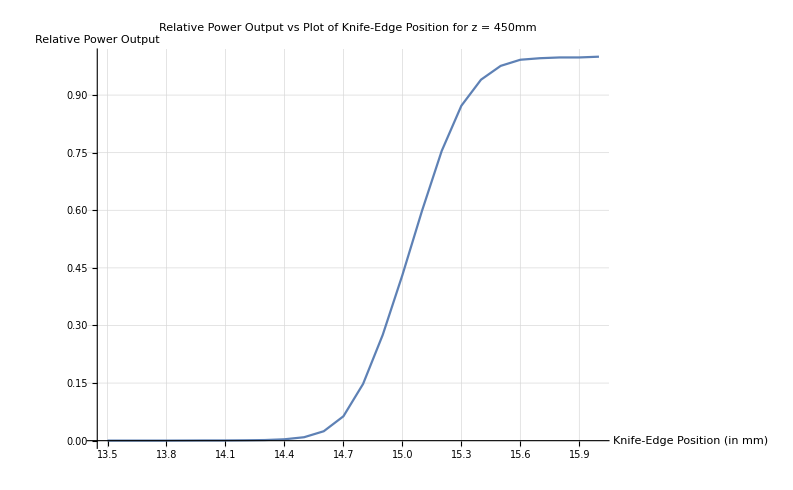

```mathematica
ListPlot[data3, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 450mm", GridLines->Automatic]
```

```mathematica
temp = Table[4.96 * yValues3[[i]], {i, 1,Length[yValues3]}]
```

{4.96,4.9501,4.9501,4.9402,4.9204,4.8412,4.66299,4.32639,3.74228,2.97006,2.13844,1.36623,0.732615,0.314826,0.121772,0.0445509,0.0178204,0.00792016,0.0049501,0.00297006,0.00297006,0.00198004,0.00099002,0.00099002,0.00099002,0.00099002}